```mathematica
params={g->9.8, c->0.05, m->1};
t0 = 0;
tf=10;
```

```mathematica
vel = NDSolveValue[{D[v[t], t]==g-c/m v[t]^2,v[0]==0}/.params,v, {t,t0, tf}];
pos = NDSolveValue[{D[v[t],{t,2}]==g-c/m D[v[t],t]^2,v[0]==0, v'[0]==0}/.params, v, {t,t0, tf}];
```

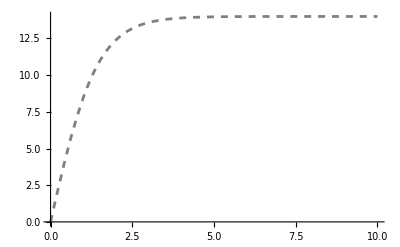

```mathematica
numSolPlot = Plot[vel[x], {x,t0, tf}, PlotStyle->{Dashed, Gray}, PlotRange->All]
```

```mathematica
vTerm=Sqrt[(m g)/c];
```

```mathematica
vAnalytic[t_]:=vTerm Tanh[(g t)/vTerm]
yAnalytic[t_]:=vTerm^2/g Log[Cosh[(g t)/vTerm]]
```

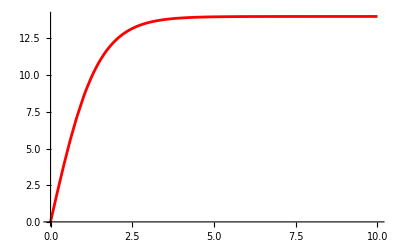

```mathematica
analSolPlot = Plot[vAnalytic[t]/.params,{t,t0, tf}, PlotStyle->Red, PlotRange->All]
```

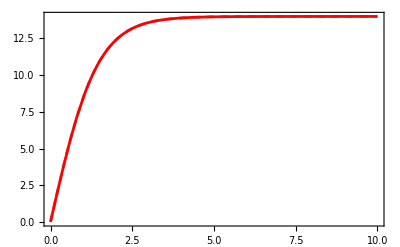

```mathematica
Show[numSolPlot, analSolPlot, Frame->True]
```

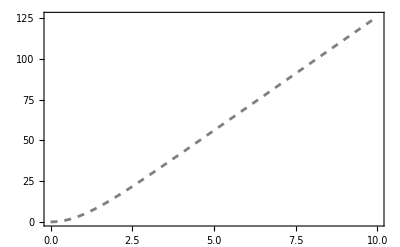

```mathematica
solNumPlot = Plot[pos[t],{t,t0, tf}, PlotStyle->{Dashed, Gray}, Frame->True]
```

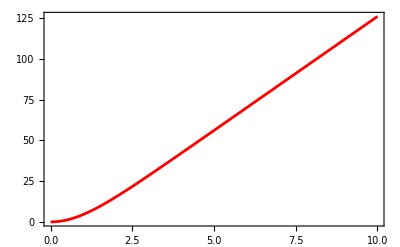

```mathematica
vAnalyticPlot = Plot[yAnalytic[t]/.params,{t,t0, tf}, PlotStyle->Red, Frame->True]
```

```mathematica
vAnalytic[t]/.params
```

14. Tanh[0.7 t]